```mathematica
ClearAll["Global`*"]
```

# Notes on J. of Comp. Phys. 228 (2009) 8712–8725

## Preliminaries

We start by considering sums of the form:
f(x_i) = ∑_(j=1)^N K(x_i,y_j)σ_j for i = 1, ..., N
in Mathematica, we can write this as

```mathematica
f[xi_,N0_]:=∑_(j=1)^N0 Ke[xi,y[j]]σ[j];(*example for N0 = 5*) f[xi,5];
```

for some observation points xi = x_i=x[i] and source points σ_j= σ[j]. The kernel is denoted by Ke. We implement a low-rank approximation to the kernel as

```mathematica
LowRankKe[x_,y_,n_]:=∑_(l=1)^n u[l,x]ν[l,y];(*example for n = 3*)LowRankKe[x,y,3];
```

Substitution of the above equation into our first equation, yields

```mathematica
LowRankf[xi_,n_,N0_]:=∑_(l=1)^n ∑_(j=1)^N0 u[l,xi]ν[l,y[j]]σ[j]
```

To implement the above equation, we need to first transform our source functions

```mathematica
W[l_,N0_]:=∑_(j=1)^N0 ν[l,y[j]]σ[j]
```

Next, we compute our low rank f(x) at each observation point with our transformed source

```mathematica
TransformedLowRankf[xi_,n_,N0_]:=Sum[u[l,xi]*W[l,N0],{l,1,n}]
```

Consider a function g(x) on a closed interval [-1,1]. This function could be x^2, Cos[x], 5x, ect. An n-point interpolant that approximates g(x) can be expressed as

```mathematica
p[n_,x_]:=Sum[g[x[l]]w[l,x],{l,1,n}]
```

for example, 4-point interpolation of x^2 with weighting functions w_l:

```mathematica
g[x_]:=x^2;p[4,x]
```

w[1,x] x[1]^2+w[2,x] x[2]^2+w[3,x] x[3]^2+w[4,x] x[4]^2

Now we can approximate the kernel with the above interpolation formula. First fix the variable y and treat the kernel as a function of x

```mathematica
Ker[x_,y_,n_]:=Sum[Ke[x[l],y]w[l,x],{l,1,n}]; ClearAll[Ker];
```

We then use the interpolation formula again to get

```mathematica
Ker[x_,y_,n_]:=Sum[Sum[Ke[x[l],y[m]]w[l,x]w[m,y],{l,1,n}],{m,1,n}]
```

This can indeed be checked again to verify that it is a low-rank representation of the kernel K(x,y) with
u_l(x) = w_l(x) and ν_l(y) = Sum[K(x[l],y[m]),{m,1,n}]. Note that any interpolation scheme can be used to construct a low-rank approximation, we can turn to the Chebyshev polynomials. They will serve as the interpolation basis with their roots as the interpolation nodes. Mathematica implements the Chebyshev polynomials as ChebyshevT[n,x] (first-kind and order n), ie

```mathematica
ChebyshevT[2,x]
```

-1+2 x^2

Note that the domain of ChebyshevT[n,x] for x = Cos[θ], θ ∈ [0,2π] is closed on T_n[x] ∈ [-1,1]:

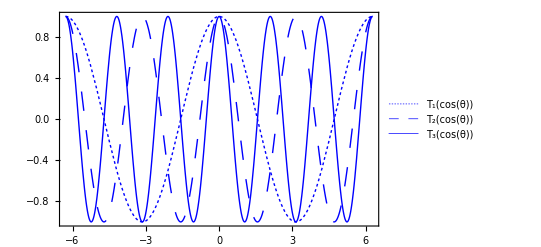

```mathematica
Plot[{ChebyshevT[1,Cos[θ]],ChebyshevT[2,Cos[θ]],ChebyshevT[3,Cos[θ]]},{θ,-2π,2π},PlotLegends->"Expressions",PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},Frame->True]
```

### Roots:

The roots of the Chebyshev polynomials are located at specific points. T_n(x)  has n roots located at

```mathematica
Solve[ChebyshevT[1,Cos[θ]]==0,θ]
```

{{θ→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[ChebyshevT[2,Cos[θ]]==0,θ]
```

{{θ→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[-π/4+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[(3 π)/4+2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[ChebyshevT[3,Cos[θ]]==0,θ]
```

{{θ→ConditionalExpression[-(5 π)/6+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[-π/6+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π/6+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[(5 π)/6+2 π C[1],C[1]∈Integers]}}

Clearly, this follows a pattern. θ_m = ((2m-1)π)/(2n) for m = 1, ..., n

### Extrema:

We can also find the extrema of these functions.

```mathematica
Solve[D[ChebyshevT[1,Cos[θ]],θ]==0,θ]
```

{{θ→ConditionalExpression[2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[D[ChebyshevT[2,Cos[θ]],θ]==0,θ]
```

{{θ→ConditionalExpression[2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}

θ follows (m π)/n for T_n = (-1)^m for m = 0, ..., n

## Interpolation scheme

We now use the Chebyshev nodes(set of all roots and extrema of T_n(x)) as our interpolation nodes, the approximating polynomial p_(n-1)(x) to the function g(x) can be expressed as a sum of the Chebyshev polynomials.

```mathematica
p[n_,x_]:=1/n Sum[g[x[n,l]],{l,1,n}]+Sum[(2/n Sum[g[x[n,l]]ChebyshevT[k,x[n,l]],{l,1,n}])ChebyshevT[k,x],{k,1,n-1}]
```

where x[n, l ] are the roots of T_n[x]. Note that these roots are well-known and have closed form expressions

```mathematica
xroots[n_,l_] := Cos[(2l-1)/(2n)π];yroots[n_,l_] := Cos[(2l-1)/(2n)π]
```

Rearranging the above, we have

```mathematica
p[n_,x_]:=Sum[g[xroots[n,l]](1/n+2/n Sum[ChebyshevT[k,xroots[n,l]]ChebyshevT[k,x],{k,1,n-1}]),{l,1,n}]
```

Can now look at the interpolation of some function. Let’s use g(x)=x^5

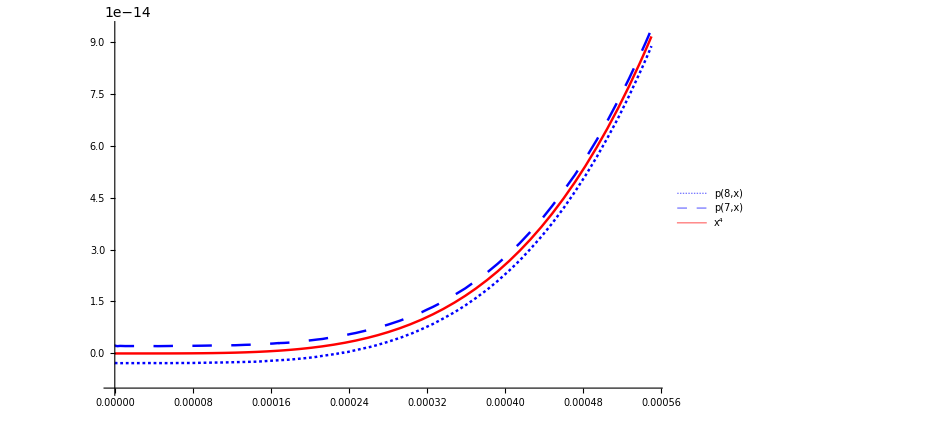
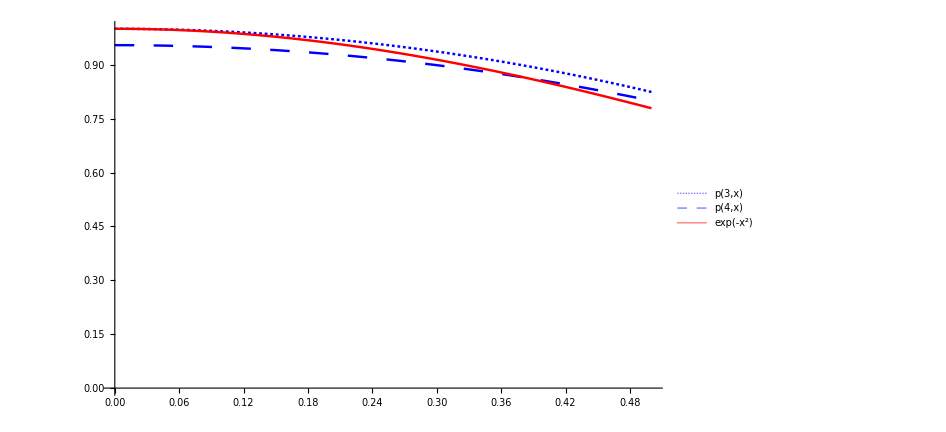

```mathematica
{g[x_]:=x^4;Plot[{p[8,x],p[7,x],x^4},{x,0,0.00055},PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Red,Thickness[0.0025]}},ImageSize->700,PlotLegends->"Expressions",AxesOrigin->{0,-1*10^-14}],g[x_]:=Exp[-x^2];Plot[{p[3,x],p[4,x],Exp[-x^2]},{x,0,0.5},PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Red,Thickness[0.0025]}},ImageSize->700,PlotLegends->"Expressions",AxesOrigin->{0,-1*10^-14}]}
```

and errors as a function of x

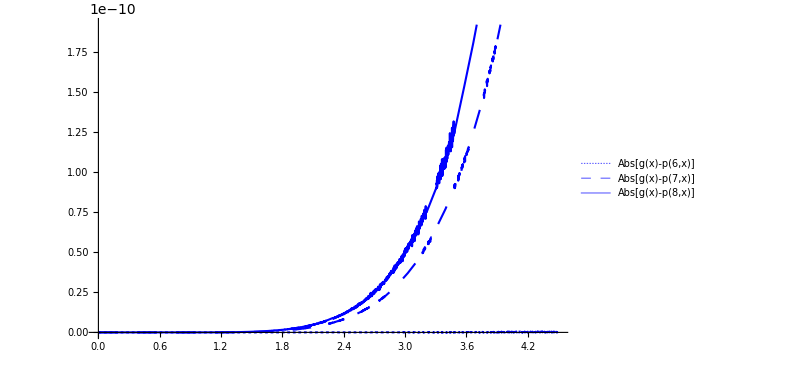
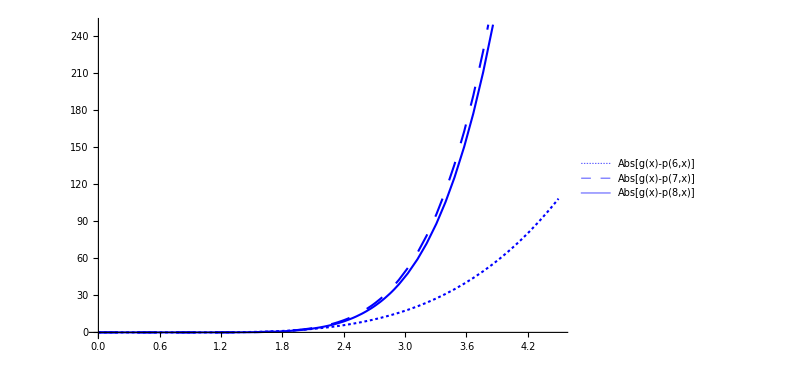

```mathematica
{g[x_]:=x^4;Plot[{Abs[g[x]-p[6,x]],Abs[g[x]-p[7,x]],Abs[g[x]-p[8,x]]},{x,0,4.5},PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},ImageSize->600,PlotLegends->"Expressions"],g[x_]:=Exp[-x^2];Plot[{Abs[g[x]-p[6,x]],Abs[g[x]-p[7,x]],Abs[g[x]-p[8,x]]},{x,0,4.5},PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},ImageSize->600,PlotLegends->"Expressions"]}
```

```mathematica
(*can compare some other interpolation schema*)
```

Very much near exact for n - 1 > leading order of polynomial. Error does in fact grow with the larger orders as stated in this work. Turns out, the convergence properties of these functions are very good.  See the paper for more details. Anyway, now that it is clear that the interpolation scheme is useful, we can write a interpolation scheme for our low-rank kernel. We’ll stick to 1D for now

## Low-rank kernel, Chebyshev interpolation

```mathematica
S[n_,x_,y_]:=1/n+2/n Sum[ChebyshevT[k,x]ChebyshevT[k,y],{k,1,n-1}]
```

Using (6) from this work, we can write

```mathematica
f[xi_,n_,N0_]:=Sum[Sum[Sum[S[n,xroots[n,l],xi]Ke[xroots[n,l],yroots[n,m]] σ[j]S[n,yroots[n,m],y[j]],{j,1,N0}],{m,1,n}],{l,1,n}](*y[j] and σ[j] need to be known, and the kernel also needs to be defined*)
```

for some source points y_j and observation points x_i. In order to implement the above sum, one needs to decompose the above triple sum in steps. First we find the weights at the Chebyshev nodes y_m (yroots[n,m]) by

```mathematica
W[N0_,n_,m_]:=Sum[σ[j] S[n,yroots[n,m],y[j]],{j,1,N0}]
```

Next, we take that weight, and compute f(x) at each of the nodes to give f(x_l):

```mathematica
fnode[l_,n_,N0_]:=Sum[W[N0,n,m]Ke[xroots[n,l],yroots[n,m]],{m,1,n}]
```

Finally, we compute the function f(x) at the observation points x_i by interpolation using S_n

```mathematica
f[xi_,n_,N0_]:=Sum[fnode[l,n,N0]S[n,xroots[n,l],xi],{l,1,n}]
```

This method has specific predictions for the computational cost of each step. We can test these if we know y[j], σ[j] and Ke[x,y].

### 3D low-rank Chebyshev interpolation:

The low-rank approximation of the kernel in 3D has nine summation indices for some target point {xt,yt,zt} and source point {xs,ys,zs} because the interpolation nodes themselves form a vector space. In the notation of the work we are studying, we use l → {l1, l2 , l3} and m→ {m1, m2, m3} . It is a rather formidable sum.

```mathematica
R[n_,xt_,yt_,zt_,xs_,ys_,zs_]:=S[n,xt,xs]S[n,yt,ys]S[n,zt,zs]
```

```mathematica
xtroot[n_,l_] := Cos[(2l-1)/(2n)π];ytroot[n_,l_] := Cos[(2l-1)/(2n)π];ztroot[n_,l_] := Cos[(2l-1)/(2n)π];xsroot[n_,l_] := Cos[(2l-1)/(2n)π];ysroot[n_,l_] := Cos[(2l-1)/(2n)π];zsroot[n_,l_] := Cos[(2l-1)/(2n)π];
```

```mathematica
LowRank3DKe[n_,xt_,yt_,zt_,xs_,ys_,zs_]:=Sum[Sum[Sum[Sum[Sum[Sum[Ke[xtroot[n,l1],ytroot[n,l2],ztroot[n,l3],xsroot[n,m1],ysroot[n,m2],zsroot[n,m3]]R[n,xtroot[n,l1],ytroot[n,l2],ztroot[n,l3],xt,yt,zt]R[n,xsroot[n,m1],ysroot[n,m2],zsroot[n,m3],xs,ys,zs],{l1,1,n}],{l2,1,n}],{l3,1,n}],{m1,1,n}],{m2,1,n}],{m3,1,n}]
```

We will implement a continuous kernel of dim 3 to test the predictions of the computational costs. Let’s use a 1/r^4 kernel.

```mathematica
Ke[xt_,yt_,zt_,xs_,ys_,zs_]:=(1/((xt-xs)+(yt-ys)+(zt-zs)))^3
```

```mathematica
LowRank3DKe[3,xt,0.1,0.1,0.1,0.1,0.1]
```

Power::infy: Infinite expression 1/0 encountered.

Part::pkspec1: The expression √3/2 cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

ReplaceAll::reps: {« 1 » ⟦ 3, √3/2, 1 + xt, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {« 1 » ⟦ 3, √3/2, xt, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

## Further work:

Now we look into how to implement this interpolation scheme in 3D. Then further work will be done to extend the notion of N body particles to an N node finite element scheme and finally portability to a suitable FEM framework: libMesh.